```mathematica
a=Import["ExampleData/coneflower.jpg","Data"];
b=Import["ExampleData/coneflower.jpg"];
dim=Dimensions[a]
```

{113,150,3}

```mathematica
a=Import["ExampleData/spikey3.bmp","Data"];
b=Import["ExampleData/spikey3.bmp"];
dim=Dimensions[a]
```

{108,120,3}

```mathematica
nx=dim⟦1⟧;
ny=dim⟦2⟧;
xmax = 0.5;
xmin=0.1;
ymax=0.5;
ymin=0.1;
θmin=π/8;
θmax=7π/8;
rmin=2;
rmax=5;
t1[x_]:={(x⟦1⟧-1)/(nx-1)(xmax-xmin)+xmin,(x⟦2⟧-1)/(ny-1)(ymax-ymin)+ymin}
r2c[x_]:={x⟦1⟧Cos[x⟦2⟧],x⟦1⟧Sin[x⟦2⟧]}
g[x_]:=r2c[{(x⟦2⟧-ymin)/(ymax-ymin)(rmax-rmin)+rmin,(x⟦1⟧-xmin)/(xmax-xmin)(θmax-θmin)+θmin}]
```

```mathematica
r=0;
t=Flatten[Table[pt = {t1[{n1,n2}],t1[{n1,n2+1}],t1[{n1+1,n2+1}],t1[{n1+1,n2}]};
If[Norm[pt⟦1⟧]>r ,
pt=Map[g,pt];
color=RGBColor[a⟦n1,n2⟧⟦1⟧/256.,a⟦n1,n2⟧⟦2⟧/256.,a⟦n1,n2⟧⟦3⟧/256.];
{color,EdgeForm[{Thin,color}],Polygon[pt]}
,{}]
,{n1,1,nx},{n2,1,ny}]];
g1=Graphics[t];
```

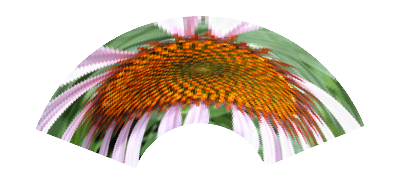

```mathematica
GraphicsRow[{g1,b}]
```